## Transistor Sizes

```mathematica
Xbk=XA10={6.*10^-7,1.96*10^-6};
Xm=XA1={9.2*10^-7,5.01*10^-6};
XA3=XA4={6.*10^-7,4.12*10^-6};
XA2=XA5=XA6={6.*10^-7,1.36*10^-6};
XB2={6.93*10^-7,1.85*10^-6};
XB3={6.5*10^-7,3.33*10^-6};
XA12={6.5*10^-7,3.3*10^-6};
XA8={9*10^-7,7.3*10^-7};
Xlk=XB1=XA7= {6.5*10^-7,4.33*10^-6};
(*XA2=XA5=XA6=XA3=XA4={6.*10^-7,1.36*10^-6};*)
(*Xlk=XB1=XB2 =XB3=XA1=XA10=XA12=XA7= Xm=Xbk={6.5*10^-7,4.33*10^-6};*)
TransistorList={XB1,XB2,XA1,XA2,XA3,XA4,XA5,XA6,XA7,XA8,XA10,XA12};
```

## Alpha Values

```mathematica
α=#⟦1⟧/#⟦2⟧&;
alphaList=α[#]&/@TransistorList
```

{0.150115,0.374595,0.183633,0.441176,0.145631,0.145631,0.441176,0.441176,0.150115,1.23288,0.306122,0.19697}

### Width Calculator

```mathematica
WidthCalc[X_,l_]:=α[X]*l;
LengthCalc[X_,w_]:=w/α[X];
```

### Plot of α Values

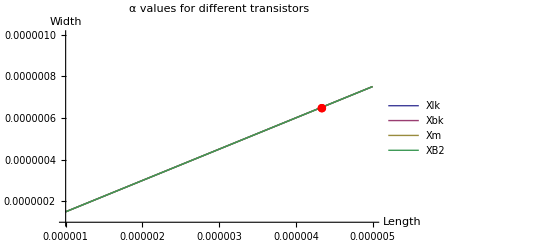

```mathematica
Show[Plot[{WidthCalc[Xlk,l],WidthCalc[Xbk,l],WidthCalc[Xm,l],WidthCalc[XB2,l]},{l,1*10^-6,5*10^-6},PlotRange->{1*10^-7,1*10^-6}, PlotLegends->{"Xlk", "Xbk", "Xm", "XB2"}, AxesLabel->{Length, Width}, PlotLabel->"α values for different transistors"],
ListPlot[{{XB2⟦2⟧,XB2⟦1⟧}},PlotStyle->Red,PlotMarkers->{"●",Medium}]]
```

## Capacitance Extraction from data from SPICE

### Soma's Capacitor

Data comes in the form of a list of {x μs, y V}
Then this script takes this list and gets the slope of the line, and uses that to calculate the capacitor’s value using the equation:
	I=C dV/dt, where dV/dtequals the slope and I is a value input by the user as I_const

#### Data Input and Massaging

```mathematica
dataSoma={{4,0.72921},{5,0.83853},{6,0.94822},{7,1.0585},{8,1.1691},{9,1.2796},{10,1.3912}};
dataSoma⟦;;,1⟧ = #*1.*10^-6&/@dataSoma⟦;;,1⟧;
lineSoma=Fit[dataSoma,{1,x},x]
```

110321. x+0.286947

#### Plot

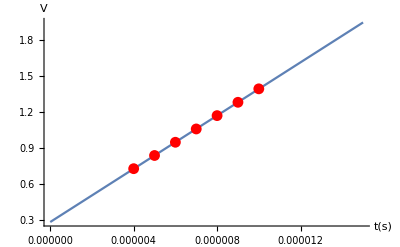

```mathematica
Show[
Plot[{lineSoma},{x,0,15*10^-6},AxesLabel->{"t(s)","V"}],
ListPlot[dataSoma, PlotStyle->Red]
]
```

#### Capacitor Value Calculation

```mathematica
IconstSoma=Quantity[10,"NanoAmps"];
dvdtSoma=Quantity[lineSoma[[2,1]],"Volts/Seconds"];
Cm=UnitConvert[UnitSimplify[IconstSoma/dvdtSoma],"FemtoFarads"];
Row[{"C_m: ", Cm}]
```

C_m: 90.6445

### Capacitance Extraction from data from SPICE (for refractory)

Data comes in the form of a list of {x μs, y V}
Then this script takes this list and gets the slope of the line, and uses that to calculate the capacitor’s value using the equation:
	I=C dV/dt, where dV/dtequals the slope and I is a value input by the user as Iconst

#### Data Input and Massaging

```mathematica
dataRef={{4,1.066},{5,1.2604},{6,1.4571},{7,1.6541},{8,1.8515},{9,2.0516},{10,2.2516},{15,3.2695},{20,4.3123},{25,5.3776},{30,6.4609},{35,7.5519},{40,8.6291},{45,9.6686},{50,10.667}};
dataRef⟦;;,1⟧ = #*1.*10^-6&/@dataRef⟦;;,1⟧;
lineRef=Fit[dataRef⟦1;;7⟧,{1,x},x]
```

197629. x+0.272643

#### Plot

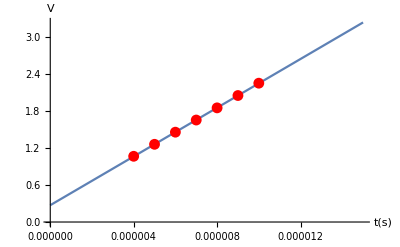

```mathematica
Show[
Plot[{lineRef},{x,0,15*10^-6},AxesLabel->{"t(s)","V"}],
ListPlot[dataRef⟦1;;7⟧, PlotStyle->Red]
]
```

```mathematica
lineRef[[2,1]]
```

197629.

#### Capacitor Value Calculation

```mathematica
IconstRef=Quantity[10,"NanoAmps"];
dvdtRef=Quantity[lineRef[[2,1]],"Volts/Seconds"];
Cref=UnitConvert[UnitSimplify[IconstRef/dvdtRef],"FemtoFarads"];
Row[{"C_ref: ", Cref}]
```

C_ref: 50.6

```mathematica
Ut[25]
```

0.025693

## Calibration Parameters (Revised Formula 3)

This set of calibration parameters now also has t_r compensation, which takes into account that the circuit doesn’t fully reset under varying conditions of I_in and I_lk.  It also folds all of the ρ_ref parameters into as few parameters as possible.  This also means that, unlike Formula 2 below, it doesn’t ensure that the calibration parameters are independent.v

```mathematica
Vdd=Quantity[1.8, "Volts"];
I0M=Quantity[8,"FemtoAmps"]/(Quantity[1.1,"MicroAmp"]/1024);
I08=I0M*α[XA8]/α[XA1];
Ut[T_]:=UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]];
pquaR3=(2α[XA4]α[XA1]α[XA10]α[XB1])/(α[XA7]^2 α[XB2]α[XA3]);
ptauR3[kappa_]:=α[XB1]/α[XA7](Cm*Ut[25])/kappa;
pilkrR3=α[XB1]/α[XA7] I08;
pref1R3[kappa_]:=(α[XB3]Cref)/α[XA12](Vdd-Ut[25]/kappa Log[(α[XA10]α[XA1])/(α[XB1]α[XB2]α[XA8]I08 I0M)]);
pref2R3[kappa_]:=(α[XB3]Cref)/α[XA12] Ut[25]/kappa;
```

```mathematica
Grid[
{{"ρ_qua: ", pquaR3,"ρ_tau: ", ptauR3[κ],"ρ_ilkr: ",pilkrR3},
{"ρ_ref1: ", pref1R3[κ],"ρ_ref2: ",pref2R3[κ]}}
]/.κ->.687
```

ρ_qua:  | 1.99935 | ρ_tau:  | 3.38994 | ρ_ilkr:  | 0.0000499996
ρ_ref1:  | 49.9377 | ρ_ref2:  | 1.8753 |  |

## Calibration Parameters (Revised Formula 2)

This set of calibration parameters now also has t_r compensation, which takes into account that the circuit doesn’t fully reset under varying conditions of I_in and I_lk

```mathematica
Vdd=Quantity[1.8, "Volts"];
I0M=Quantity[8,"FemtoAmps"]/(Quantity[1.1,"MicroAmp"]/1024);
I08=I0M*α[XA8]/α[XA1];
Ut[T_]:=UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]];
pquaR2=(2α[XA4]α[XA1]α[XA10])/(α[XA7]α[XB2]α[XA3]);
ptauR2[kappa_]:=(Cm*Ut[25])/kappa;
pilkrR2=I08;
plkbR2=α[XB1]/α[XA7];
prefbR2=(α[XB3]Cref)/α[XA12];
pref1R2=Vdd;
pref2R2[kappa_]:=Ut[25]/kappa;
pref3R2=(α[XA10]α[XA1])/(α[XB1]α[XB2]α[XA8]I08 I0M);
```

```mathematica
Grid[
{{"ρ_qua: ", pquaR2,"ρ_tau: ", ptauR2[κ]},
{"ρ_ilkr: ",pilkrR2,"ρ_lkb: ",plkbR2},
{"ρ_refb: ", prefbR2,"ρ_ref1: ", pref1R2},
{"ρ_ref2: ",pref2R2[κ],"ρ_ref3: ",pref3R2}}
]/.κ->.687
```

ρ_qua:  | 1.99935 | ρ_tau:  | 3.38994
ρ_ilkr:  | 0.0000499996 | ρ_lkb:  | 1.
ρ_refb:  | 50.1441 | ρ_ref1:  | 1.8
ρ_ref2:  | 0.0373982 | ρ_ref3:  | 2.17758×10^9

## Calibration Parameters (Revised Formula)

This section can be used to calculate the calibration parameters using the new revised derivation of the dynamical systems equations.  These equations account for the leakage current caused by I_lkr

```mathematica
Vdd=Quantity[1.8, "Volts"];
Ut[T_]:=UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]];
pquaR=(2α[XB1]α[XA4]α[XA1]α[XA10])/(α[XA7]^2 α[XB2]α[XA3]);
ptauR[kappa_]:=(α[XB1]*Cm*Ut[25])/(α[XA7]kappa);
prefR=(α[XB3](Cref Vdd))/α[XA12];
IinputR[ιin_,Ilk_,Ilkr_]:=(ιin (Ilk)(1+α[XB1]/α[XA7] Quantity[Ilkr,"FemtoAmps"]/Ilk)^2)/pquaR;
IleakR[τm_,kappa_,Ilkr_]:=UnitConvert[Quantity[ptauR[kappa]/Quantity[τm,"Seconds"] -α[XB1]/α[XA7] Quantity[Ilkr,"FemtoAmps"]],"FemtoAmps"];
IrefR[tref_]:=UnitConvert[Quantity[prefR/Quantity[tref,"Seconds"]],"PicoAmps"];

ιinCalcR[Iin_,Ilk_,Ilkr_]:=pquaR Iin/(Ilk(1+α[XB1]/α[XA7] Ilkr/Ilk)^2);
τCalcR[Ilk_,kappa_,Ilkr_]:=UnitConvert[Quantity[ptauR[kappa]/(Quantity[Ilk,"FemtoAmps"](1+α[XB1]/α[XA7] Quantity[Ilkr,"FemtoAmps"]/Quantity[Ilk,"FemtoAmps"]))],"Seconds"];
trefCalcR[Iref_]:=UnitConvert[Quantity[prefR/Quantity[Iref,"PicoAmps"]],"Seconds"];
Manipulate[
Grid[{{
Grid[{{"ρ_qua: ", pquaR},{"ρ_tau: ", ptauR[κ1]},{"ρ_ref: ",prefR}}],
Manipulate[
Grid[{
{"I_input: ", IinputR[ιin,IleakR[τ,κ1,Ilkref],Ilkref]},
{"I_leak: ",IleakR[τ,κ1,Ilkref]},
{"I_ref: ",IrefR[tref]}
}],(*Grid*)
{{ιin,0.5,"i_in"},0,2.0,0.00005,Appearance->{"Labeled","Open"}},
{{τ,0.01,"τ_m"},0.001,0.050,0.001,Appearance->{"Labeled","Open"}},
{{tref,0.001,"t_ref"},0.001,0.02,0.001,Appearance->{"Labeled","Open"}},
{{Ilkref,11.16,"I_lkref"},.100,20,.5,Appearance->{"Labeled","Open"}}
(*{{κ1,0.6,"κ"},{0.4,0.5,0.6,0.7}}*)
](*Manipulate*),
Manipulate[
Grid[{
{"ι_in: ", ιinCalcR[Iin,Ilk,Ilkref]},
{"τ_m: ",τCalcR[Ilk,κ1,Ilkref]},
{"t_ref: ",trefCalcR[Iref]}
}],(*Grid*)
{{Iin,87.6443,"I_in"},10,10000,10,Appearance->{"Labeled","Open"}},
{{Ilk,327.794,"I_lk"},100,4000,10,Appearance-> {"Labeled","Open"}},
{{Iref,91.0799,"I_ref"},10,10000,10,Appearance->{"Labeled","Open"}},
{{Ilkref,11.2,"I_lkref"},.100,20,.5,Appearance->{"Labeled","Open"}}
(*{{κ1,0.7,"κ"},{0.4,0.5,0.6,0.7}}*)
](*Manipulate*)
}}
],
{{κ1,0.687,"κ"},{0.668,0.684,0.685,0.686,0.687,0.688,0.689,0.690,0.691,0.692}},LabelStyle->Large]
```

```mathematica
α[XA7]
α[XB1]
```

0.150115

0.150115

## Calibration Parameters

```mathematica
Vdd=Quantity[1.8, "Volts"];
Ut[T_]:=UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]];
pqua=(2α[XB1]α[XA6]α[XA1]α[XA10])/(α[XA7]^2 α[XB2](α[XA4]+α[XA6]));
ptau[kappa_]:=(α[XB1]*Cm*Ut[25])/(α[XA7] kappa);
pref=(Cref Vdd)/α[XA12];
Ileak[τm_,kappa_]:=UnitConvert[Quantity[ptau[kappa]/Quantity[τm,"Seconds"]],"FemtoAmps"];
Iinput[ιin_,Ilk_]:=UnitConvert[(ιin Ilk)/pqua,"FemtoAmps"];
Iref[tref_]:=UnitConvert[Quantity[pref/Quantity[tref,"Seconds"]],"PicoAmps"];
τCalc[Ilk_,kappa_]:=UnitConvert[Quantity[ptau[kappa]/Quantity[Ilk,"FemtoAmps"]],"Seconds"];
ιinCalc[Iin_,Ilk_]:=pqua Iin/Ilk;
trefCalc[Iref_]:=UnitConvert[Quantity[pref/Quantity[Iref,"PicoAmps"]],"Seconds"];
Manipulate[
Grid[{{
Grid[{{"ρ_qua: ", pqua},{"ρ_tau: ", ptau[κ1]},{"ρ_ref: ",pref}}],
Manipulate[
Grid[{
{"I_input: ", Iinput[ιin,Ileak[τ,κ1]]},
{"I_leak: ",Ileak[τ,κ1]},
{"I_ref: ",Iref[tref]}
}],(*Grid*)
{{ιin,0.518,"i_in"},0,2.0,0.00005,Appearance->{"Labeled","Open"}},
{{τ,0.01,"τ_m"},0.001,0.050,0.001,Appearance->{"Labeled","Open"}},
{{tref,0.001,"t_ref"},0.001,0.02,0.001,Appearance->{"Labeled","Open"}}
(*{{κ1,0.6,"κ"},{0.4,0.5,0.6,0.7}}*)
](*Manipulate*),
Manipulate[
Grid[{
{"ι_in: ", ιinCalc[Iin,Ilk]},
{"τ_m: ",τCalc[Ilk,κ1]},
{"t_ref: ",trefCalc[Iref]}
}],(*Grid*)
{{Iin,169.497,"I_in"},100,10000,10,Appearance->{"Labeled","Open"}},
{{Ilk,338.994,"I_lk"},100,4000,10,Appearance-> {"Labeled","Open"}},
{{Iref,606.733,"I_ref"},100,10000,10,Appearance->{"Labeled","Open"}}
(*{{κ1,0.7,"κ"},{0.4,0.5,0.6,0.7}}*)
](*Manipulate*)
}}
],
{{κ1,0.687,"κ"},{0.668,0.684,0.685,0.686,0.687,0.688,0.689,0.690,0.691,0.692}},LabelStyle->Large]
```

## Current Bias Values

```mathematica
Ilk=3.5*10^-9;
Iin=10*10^-9;
Ibk=3.5*10^-9
Isoma=α[Xm]*(α[Xbk]/Ibk)*((Ilk*Iin)/(α[Xlk]*α[XB2]))
```

3.5×10^-9

9.99674×10^-9

## Old/Obsolete

### Calculate Capacitance Value using Time Constant

Vc=Vs(1-E^(-t/(R C)))
Vc/Vs=1-E^(-t/(R C))
E^(-t/(R C))=1-Vc/Vs
-t/(R C)=Log[1-Vc/Vs]

```mathematica
CapVal[Vc_, Vs_,t_, R_]:=-t/(R Log[1-Vc/Vs]);
```

```mathematica
CapVal[ 5.0, 10,55.118*10^-12, 1000]
CapVal[ 9.0, 10,194.51*10^-12, 1000]
CapVal[ 9.9, 10,403.39*10^-12, 1000]
```

7.95185×10^-14

8.44746×10^-14

8.7595×10^-14

```mathematica
CapVal[ 0.5, 1,25.128*10^-12, 1000]
CapVal[0.632, 1,55.167*10^-12, 1000]
CapVal[0.9, 1,183.71*10^-12, 1000]
CapVal[ 0.99, 1,414.12*10^-12, 1000]
```

3.6252×10^-14

5.51851×10^-14

7.97842×10^-14

8.9925×10^-14